This is the third of three notebooks which accompany the paper “Gravitational Waves on Kerr Black Holes II: SUBTITLE” [arxiv link]. This notebook imports the results of MetricPerturbations.nb and shows how to plot a tetrad or coordinate component of the metric perturbation. This notebook uses the SpinWeightedSpheroidalHarmonics package from the BHPToolkit, which can be installed from here: https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/.

## 1. Setup and Definitions

We allow subscripts on our variables, and set the working directory to this notebook’s path.

```mathematica
(*<<SpinWeightedSpheroidalHarmonics`*)
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
SetDirectory@NotebookDirectory[];
```

We define various useful symbols, as well as the metric and tetrad vectors in Boyer-Lindquist coordinates.

```mathematica
$Assumptions = {
0 < a , 
0<M,
0<r,
Element[Λ, Reals], 
Element[a, Reals],
Element[M, Reals],  
Element[t, Reals], 
Element[r, Reals],
Element[θ, Reals],  
Element[ϕ, Reals],
Element[m,Reals],
Element[s,Reals]
};
coord={t,r,θ,ϕ};
Ξ=1+Λ/3*a^2;
Δθ=1+Λ/3*a^2*Cos[θ]^2;
Σ=r^2+a^2*Cos[θ]^2;
ζ=r-ⅈ*a*Cos[θ];
ζbar=r+ⅈ*a*Cos[θ];
ωsub={Conjugate[ω]->ωbar,Conjugate[ωbar]->ω};
K[ω_,m_]:=(r^2+a^2)*ω-a*m;
Kbar[ω_,m_]:=(r^2+a^2)*Conjugate[ω]-a*m/.ωsub;
Q[ω_,m_]:=-a*ω*Sin[θ]+m*Csc[θ];
Qbar[ω_,m_]:=-a*Conjugate[ω]*Sin[θ]+m*Csc[θ]/.ωsub;
gBL=ϵg*{{-(Δ[r]-Δθ*a^2 Sin[θ]^2)/(Ξ^2*Σ),0,0,-(a*Sin[θ]^2)/(Ξ^2*Σ)(-Δ[r]+Δθ*(r^2+a^2))},{0,Σ/Δ[r],0,0},{0,0,Σ/Δθ,0},{-(a*Sin[θ]^2)/(Ξ^2*Σ)(-Δ[r]+Δθ*(r^2+a^2)),0,0,((Δθ*((r)^2+a^2)^2-Δ[r]*a^2*Sin[θ]^2)/(Σ*Ξ^2))*Sin[θ]^2}};
lupBL={Ξ*(r^2+a^2)/Δ[r],1,0,(a*Ξ)/Δ[r]};
nupBL=1/(2*Σ)*{Ξ*(r^2+a^2),-Δ[r],0,a*Ξ};
mupBL=1/(Sqrt[2Δθ]*ζbar)*{I*a*Ξ*Sin[θ],0,Δθ,I*Ξ/Sin[θ]};
mbarupBL=1/(Sqrt[2Δθ]*ζ)*{-I*a*Ξ*Sin[θ],0,Δθ,-I*Ξ/Sin[θ]};
ldownBL=gBL.lupBL//Simplify;
ndownBL=gBL.nupBL//Simplify;
mdownBL=gBL.mupBL//Simplify;
mbardownBL=gBL.mbarupBL//Simplify;
```

## 2. Radial and Angular Mode Functions

We define the radial and angular Teukolsky equations.

```mathematica
eqR=Δ[r]^-s*D[Δ[r]^(s+1)*D[R[s,ω,l,m,r],r],r]+((Ξ^2*K[ω,m]^2-s*I*Ξ*K[ω,m]*Δ'[r])/Δ[r]+4I*s*ω*Ξ*r+s*Δ''[r]-2(2s-1)*(s-1)*Λ/3*r^2+s/3 a^2 Λ)*R[s,ω,l,m,r]-(λ[s,ω,l,m]+2s)*R[s,ω,l,m,r];
eqS=1/Sin[θ] D[Δθ*Sin[θ]*D[S[s,ω,l,m,θ],θ],θ]+(ω^2*Ξ^2(-(a^2*Sin[θ]^2)/Δθ)+2*m*ω*a*Ξ^2/Δθ+m^2*Ξ^2(-1/Sin[θ]^2+(a^2*Λ)/(3Δθ) *Cot[θ]^2)-2ω*s*a*Ξ^2*Cos[θ]/Δθ-2m*s*Ξ*(2-Ξ/Δθ)Cos[θ]/Sin[θ]^2-2(2 s^2+1)*Λ/3*a^2*Cos[θ]^2-(+s^2*Δθ*(D[Δθ,θ]/(2Δθ)+Cot[θ])^2)+λ[s,ω,l,m]+s)*S[s,ω,l,m,θ];
eqRbar=Δ[r]^-s*D[Δ[r]^(s+1)*D[Rbar[s,ω,l,m,r],r],r]+((Ξ^2*Kbar[ω,m]^2+s*I*Ξ*Kbar[ω,m]*Δ'[r])/Δ[r]-4I*s*ωbar*Ξ*r+s*Δ''[r]-2(2s-1)*(s-1)*Λ/3*r^2+s/3 a^2 Λ)*Rbar[s,ω,l,m,r]-(λbar[s,ω,l,m]+2s)*Rbar[s,ω,l,m,r];
eqSbar=1/Sin[θ] D[Δθ*Sin[θ]*D[Sbar[s,ω,l,m,θ],θ],θ]+(ωbar^2*Ξ^2(-(a^2*Sin[θ]^2)/Δθ)+2*m*ωbar*a*Ξ^2/Δθ+m^2*Ξ^2(-1/Sin[θ]^2+(a^2*Λ)/(3Δθ) *Cot[θ]^2)-2ωbar*s*a*Ξ^2*Cos[θ]/Δθ-2m*s*Ξ*(2-Ξ/Δθ)Cos[θ]/Sin[θ]^2-2(2 s^2+1)*Λ/3*a^2*Cos[θ]^2-(s^2*Δθ*(D[Δθ,θ]/(2Δθ)+Cot[θ])^2)+λbar[s,ω,l,m]+s)*Sbar[s,ω,l,m,θ];
```

Using the above equations of motion, we define rules to remove second radial and angular derivatives of the mode functions. We then check that these rules yield zero when applied to the equations of motion.

```mathematica
Rsub={D[R[s0_,ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[D[R[s,ω,l,m,r],{r,2}]/.Solve[eqR==0,D[R[s,ω,l,m,r],{r,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],l->l0,m->m0},D[Rbar[s0_,ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[D[Rbar[s,ω,l,m,r],{r,2}]/.Solve[eqRbar==0,D[Rbar[s,ω,l,m,r],{r,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],m->m0}};
Ssub={D[S[s0_,ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[D[S[s,ω,l,m,θ],{θ,2}]/.Solve[eqS==0,D[S[s,ω,l,m,θ],{θ,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],l->l0,m->m0},D[Sbar[s0_,ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[D[Sbar[s,ω,l,m,θ],{θ,2}]/.Solve[eqSbar==0,D[Sbar[s,ω,l,m,θ],{θ,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],m->m0}};
```

```mathematica
{eqR==0,eqRbar==0}/.Rsub/.ωsub//Simplify
{eqS==0,eqSbar==0}/.Ssub/.ωsub//Simplify
```

{True,True}

{True,True}

## 3. Radial and Angular Modes in Terms of Heun Functions

### Angular Modes

We define explicit solutions to the angular Teukolsky equation in terms of confluent Heun functions. The normalization matches that of Eq. (2.6).

```mathematica
Shat[s_,ω_,l_,m_,θ_]:=Module[{μ1,μ2,μ3,μ3tilde,μ4,α,β,γ,q,xsplus,u},
μ1=Abs[s+m]/2;
μ2=Abs[s-m]/2;
μ3=I/2((1+(a^2 σ^2)/L^2)/((a σ)/L)*a*ω-m*(a σ)/L-ⅈ s);
μ3tilde=-I/2((1+(a^2 σ^2)/L^2)/((a σ)/L)*a*ω-m *(a σ)/L+ⅈ s);
μ4=-(μ1+μ2+μ3+1);
γ=2μ2+1;
q=ⅈ/(4(a σ)/L)(λ[s,ω,l,m]+s-2I*(a σ)/L+2a*ω*(1+(a^2 σ^2)/L^2)*(m+s)-m^2/2*(4(a^2 σ^2)/L^2+(1+I*(a σ)/L)^2)+s^2/2*(1-I*(a σ)/L)^2+2I*m*s*(a σ)/L(1+I*(a σ)/L)-(1+I*(a σ)/L)^2*(μ1+μ2+2μ2*μ1)-2I*(a σ)/L*((2 μ3+1)*γ-1));
α=(μ1+μ2+μ3+μ3tilde+1);
β=(μ1+μ2+μ3-μ3tilde+1);
xsplus=-(I*(1+I*(a σ)/L)^2)/(4*(a σ)/L);
u=Cos[θ];
(1-Cos[θ])^μ1*(1+Cos[θ])^μ2*((Cos[θ]+(ⅈ L)/(a σ))/(-1+(ⅈ L)/(a σ)))^μ3*((Cos[θ]-(ⅈ L)/(a σ))/(-1-(ⅈ L)/(a σ)))^μ4 HeunG[xsplus,q,α,β,2μ2+1,2μ1+1,(1-(ⅈ L)/(a σ))/2*(u+1)/(u-(ⅈ L)/(a σ))]
];
Shatbar[s_,ω_,l_,m_,θ_]:=Module[{μ1,μ2,μ3bar,μ3tildebar,μ4bar,αbar,βbar,γ,qbar,xsplusbar,u},
μ1=Abs[s+m]/2;
μ2=Abs[s-m]/2;
μ3bar=-I/2((1+(a^2 σbar^2)/L^2)/((a σbar)/L)*a*Conjugate[ω]-m*(a σbar)/L+ⅈ s);
μ3tildebar=I/2((1+(a^2 σbar^2)/L^2)/((a σbar)/L)*a*Conjugate[ω]-m*(a σbar)/L-ⅈ s);
μ4bar=-(μ1+μ2+μ3bar+1);
γ=2μ2+1;
qbar=-ⅈ/(4(a σbar)/L)(λbar[s,ω,l,m]+s+2I*(a σbar)/L+2a*Conjugate[ω]*(1+(a^2 σbar^2)/L^2)*(m+s)-m^2/2*(4(a^2 σbar^2)/L^2+(1-I*(a σbar)/L)^2)+s^2/2*(1+I*(a σbar)/L)^2-2I*m*s*(a σbar)/L(1-I*(a σbar)/L)-(1-I*(a σbar)/L)^2*(μ1+μ2+2μ2*μ1)+2I*(a σbar)/L*((2 μ3bar+1)*γ-1));
αbar=(μ1+μ2+μ3bar+μ3tildebar+1);
βbar=(μ1+μ2+μ3bar-μ3tildebar+1);
xsplusbar=(I*(1-I*(a σbar)/L)^2)/(4*(a σbar)/L);
u=Cos[θ];
(1-Cos[θ])^μ1*(1+Cos[θ])^μ2*((Cos[θ]-(ⅈ L)/(a σbar))/(-1-(ⅈ L)/(a σbar)))^μ3bar*((Cos[θ]+(ⅈ L)/(a σbar))/(-1+(ⅈ L)/(a σbar)))^μ4bar HeunG[xsplusbar,qbar,αbar,βbar,2μ2+1,2μ1+1,(1+(ⅈ L)/(a σbar))/2*(u+1)/(u+(ⅈ L)/(a σbar))]
];
```

We check that these functions are in fact solutions.

```mathematica
eqS==0/.Λ->3 σ^2/L^2/.S->Function[{s,ω,l,m,θ},Shat[s,ω,l,m,θ]];
{%/.σ->1,%/.σ->I}/.m->0//Simplify
eqSbar==0/.Λ->3 σ^2/L^2/.Sbar->Function[{s,ω,l,m,θ},Shatbar[s,ω,l,m,θ]]/.ωsub;
{%/.{σ->1,σbar->1},%/.{σ->I,σbar->-I}}/.m->0//Simplify
```

{True,True}

{True,True}

### Radial Modes

Subscripted definitions have to be done outside of the initialization blocks .

```mathematica
rootlist={r1,r2,r3,r4};
Δplist=Table[D[-Λ/3*(r-r1)*(r-r2)*(r-r3)*(r-r4),r]/.r->rootlist[[i]],{i,1,4}];
Subscript[C, 1]=(Ξ*(r1^2+a^2))/Δplist[[1]];
Subscript[C, 2]=(Ξ*(r2^2+a^2))/Δplist[[2]];
Subscript[C, 3]=(Ξ*(r3^2+a^2))/Δplist[[3]];
Subscript[C, 4]=(Ξ*(r4^2+a^2))/Δplist[[4]];
Subscript[Ω, 1]=a/(r1^2+a^2);
Subscript[Ω, 2]=a/(r2^2+a^2);
Subscript[Ω, 3]=a/(r3^2+a^2);
Subscript[Ω, 4]=a/(r4^2+a^2);
```

```mathematica
Vieta1=Total[rootlist];
Vieta2=Sum[Sum[rootlist[[i]]*rootlist[[j]],{i,1,j-1}],{j,1,4}]-(a^2-σ^2*L^2);
Vieta3=Sum[Sum[Sum[rootlist[[i]]*rootlist[[j]]*rootlist[[k]],{k,1,j-1}],{j,1,i-1}],{i,1,4}]-(-2*M*σ^2*L^2);
Vieta4=r1 r2 r3 r4-(-a^2*σ^2*L^2);
```

We define explicit solutions to the radial Teukolsky equation in terms of confluent Heun functions. The normalization matches that of Eq. (2.17).

```mathematica
Rhatin[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,ξ3,ξ4,γ,δ,α,β,q,D,zinfplus,zsplus},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
α=ξ1+ξ2+ξ3+2s+1+1/2*(-s+I*((2*(1+a^2*Λ/3)*a^2*(ω(r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))-I*s));
β=ξ1+ξ2+ξ3+2s+1+1/2*(-s-I*((2*(1+a^2*Λ/3)*a^2*(ω(r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))-I*s));
D=(r1-r2)^2(r1-r3)^2(r1-r4)^2 (r2-r3)^2(r2-r4)^2 (r3-r4)^2;
q=-(-(18 Ξ^2)/(D Λ^2)*((r2-r3)^2*(r2-r4)^2*(r1-r4)*(r3-r4))/(r1-r2)*(-ω^2*r1^3 (r1 r2-2 r2 r3+r1 r3)+2a*ω*(a*ω-m)*r1*(r2*r3-r1^2)-a^2*(a*ω-m)^2*(2r1-r2-r3))-(6I*s*Ξ)/Λ*(ω*(r1*r4+a^2)-a*m)/((r1-r2)*(r3-r4)*(r1-r4))+(2 s+1)*(s+1)*(-(2*r4^2)/((r1-r2) (r3-r4))-zinfplus)-2ξ1*(zsplus*ξ2+ξ3)-(s+1)*((1+zsplus)*ξ1+zsplus*ξ2+ξ3)-(3(λ[s,ω,l,m]+(Ξ-1)*s))/(Λ*(r1-r2)*(r3-r4)));
ξ1=ⅈ Subscript[C, 1](ω-m Subscript[Ω, 1]);
ξ2=ⅈ Subscript[C, 2](ω-m Subscript[Ω, 2]);
ξ3=ⅈ Subscript[C, 3](ω-m Subscript[Ω, 3]);
ξ4=-(ξ1+ξ2+ξ3+2s+1);
zinfplus=-(r2-r4)/(r1-r2);
zsplus=-((r2-r4)/(r1-r2))*((r3-r1)/(r3-r4));
(Δplist[[1]])^-s*(r-r1)^(-ξ1-s)*((r-r2)/(r1-r2))^ξ2*((r-r3)/(r1-r3))^ξ3*((r-r4)/(r1-r4))^(2 ξ1+ξ4+s) HeunG[zsplus,q-(s+2 ξ1) (-s+α+β-2 ξ1+(-1+zsplus) (1+s+2 ξ2)),-s+β-2 ξ1,-s+α-2 ξ1,1-s-2 ξ1,1+s+2 ξ2,-((r-r1) (r2-r4))/((r1-r2) (r-r4))]
];
Rhatout[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,ξ3,ξ4,γ,δ,α,β,q,D,zinfplus,zsplus},
ξ1=ⅈ Subscript[C, 1](ω-m Subscript[Ω, 1]);
ξ2=ⅈ Subscript[C, 2](ω-m Subscript[Ω, 2]);
ξ3=ⅈ Subscript[C, 3](ω-m Subscript[Ω, 3]);
ξ4=-(ξ1+ξ2+ξ3+2s+1);
γ=2ξ1+s+1;
δ=2ξ2+s+1;
α=ξ1+ξ2+ξ3+2s+1+1/2*(-s+I*((2*(1+a^2*Λ/3)*a^2*(ω(r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))-I*s));
β=ξ1+ξ2+ξ3+2s+1+1/2*(-s-I*((2*(1+a^2*Λ/3)*a^2*(ω(r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))-I*s));
D=(r1-r2)^2(r1-r3)^2(r1-r4)^2 (r2-r3)^2(r2-r4)^2 (r3-r4)^2;
zinfplus=-(r2-r4)/(r1-r2);
zsplus=-((r2-r4)/(r1-r2))*((r3-r1)/(r3-r4));
q=-(-(18 Ξ^2)/(D Λ^2)*((r2-r3)^2*(r2-r4)^2*(r1-r4)*(r3-r4))/(r1-r2)*(-ω^2*r1^3 (r1 r2-2 r2 r3+r1 r3)+2a*ω*(a*ω-m)*r1*(r2*r3-r1^2)-a^2*(a*ω-m)^2*(2r1-r2-r3))-(6I*s*Ξ)/Λ*(ω*(r1*r4+a^2)-a*m)/((r1-r2)*(r3-r4)*(r1-r4))+(2 s+1)*(s+1)*(-(2*r4^2)/((r1-r2) (r3-r4))-zinfplus)-2ξ1*(zsplus*ξ2+ξ3)-(s+1)*((1+zsplus)*ξ1+zsplus*ξ2+ξ3)-(3(λ[s,ω,l,m]+(Ξ-1)*s))/(Λ*(r1-r2)*(r3-r4)));
(r-r1)^ξ1*((r-r2)/(r1-r2))^ξ2*((r-r3)/(r1-r3))^ξ3*((r-r4)/(r1-r4))^ξ4 HeunG[zsplus,q,α,β,2ξ1+s+1,2ξ2+s+1,-((r2-r4)(r-r1))/((r1-r2) (r-r4))]
];
Rhatinbar[s_,ω_,l_,m_,r_]:=Module[{ξ1bar,ξ2bar,ξ3bar,ξ4bar,γbar,δbar,αbar,βbar,D,qbar,zinfplus,zsplus},
ξ1bar=-ⅈ Subscript[C, 1](Conjugate[ω]-m Subscript[Ω, 1]);
ξ2bar=-ⅈ Subscript[C, 2](Conjugate[ω]-m Subscript[Ω, 2]);
ξ3bar=-ⅈ Subscript[C, 3](Conjugate[ω]-m Subscript[Ω, 3]);
ξ4bar=-(ξ1bar+ξ2bar+ξ3bar+2s+1);
γbar=2ξ1bar+s+1;
δbar=2ξ2bar+s+1;
D=(r1-r2)^2(r1-r3)^2(r1-r4)^2 (r2-r3)^2(r2-r4)^2 (r3-r4)^2;
zinfplus=-(r2-r4)/(r1-r2);
zsplus=-((r2-r4)/(r1-r2))*((r3-r1)/(r3-r4));
qbar=-(-(18 Ξ^2)/(D Λ^2)*((r2-r3)^2*(r2-r4)^2*(r1-r4)*(r3-r4))/(r1-r2)*(-Conjugate[ω]^2*r1^3 (r1 r2-2 r2 r3+r1 r3)+2a*Conjugate[ω]*(a*Conjugate[ω]-m)*r1*(r2*r3-r1^2)-a^2*(a*Conjugate[ω]-m)^2*(2r1-r2-r3))+(6I*s*Ξ)/Λ*(Conjugate[ω]*(r1*r4+a^2)-a*m)/((r1-r2)*(r3-r4)*(r1-r4))+(2 s+1)*(s+1)*(-(2*r4^2)/((r1-r2) (r3-r4))-zinfplus)-2ξ1bar*(zsplus*ξ2bar+ξ3bar)-(s+1)*((1+zsplus)*ξ1bar+zsplus*ξ2bar+ξ3bar)-(3(λbar[s,ω,l,m]+(Ξ-1)*s))/(Λ*(r1-r2)*(r3-r4)));αbar=ξ1bar+ξ2bar+ξ3bar+2s+1+1/2*(-s-I*((2*(1+a^2*Λ/3)*a^2*(Conjugate[ω](r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))+I*s));
βbar=ξ1bar+ξ2bar+ξ3bar+2s+1+1/2*(-s+I*((2*(1+a^2*Λ/3)*a^2*(Conjugate[ω](r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))+I*s));
(Δplist[[1]])^-s*(r-r1)^(-ξ1bar-s)*((r-r2)/(r1-r2))^ξ2bar*((r-r3)/(r1-r3))^ξ3bar*((r-r4)/(r1-r4))^(2 ξ1bar+ξ4bar+s)*HeunG[zsplus,qbar-(s+2 ξ1bar) (-s+αbar+βbar-2 ξ1bar+(-1+zsplus) (1+s+2 ξ2bar)),-s+βbar-2 ξ1bar,-s+αbar-2 ξ1bar,1-s-2 ξ1bar,1+s+2 ξ2bar,-((r-r1) (r2-r4))/((r1-r2) (r-r4))]/.{r3->r3bar,r4->r4bar}/.ωsub
];
Rhatoutbar[s_,ω_,l_,m_,r_]:=Module[{ξ1bar,ξ2bar,ξ3bar,ξ4bar,γbar,δbar,αbar,βbar,D,qbar,zinfplus,zsplus},
ξ1bar=-ⅈ Subscript[C, 1](Conjugate[ω]-m Subscript[Ω, 1]);
ξ2bar=-ⅈ Subscript[C, 2](Conjugate[ω]-m Subscript[Ω, 2]);
ξ3bar=-ⅈ Subscript[C, 3](Conjugate[ω]-m Subscript[Ω, 3]);
ξ4bar=-(ξ1bar+ξ2bar+ξ3bar+2s+1);
γbar=2ξ1bar+s+1;
δbar=2ξ2bar+s+1;
D=(r1-r2)^2(r1-r3)^2(r1-r4)^2 (r2-r3)^2(r2-r4)^2 (r3-r4)^2;
zinfplus=-(r2-r4)/(r1-r2);
zsplus=-((r2-r4)/(r1-r2))*((r3-r1)/(r3-r4));
qbar=-(-(18 Ξ^2)/(D Λ^2)*((r2-r3)^2*(r2-r4)^2*(r1-r4)*(r3-r4))/(r1-r2)*(-ωbar^2*r1^3 (r1 r2-2 r2 r3+r1 r3)+2a*ωbar*(a*ωbar-m)*r1*(r2*r3-r1^2)-a^2*(a*ωbar-m)^2*(2r1-r2-r3))+(6I*s*Ξ)/Λ*(ωbar*(r1*r4+a^2)-a*m)/((r1-r2)*(r3-r4)*(r1-r4))+(2 s+1)*(s+1)*(-(2*r4^2)/((r1-r2) (r3-r4))-zinfplus)-2ξ1bar*(zsplus*ξ2bar+ξ3bar)-(s+1)*((1+zsplus)*ξ1bar+zsplus*ξ2bar+ξ3bar)-(3(λbar[s,ω,l,m]+(Ξ-1)*s))/(Λ*(r1-r2)*(r3-r4)));αbar=ξ1bar+ξ2bar+ξ3bar+2s+1+1/2*(-s-I*((2*(1+a^2*Λ/3)*a^2*(ωbar(r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))+I*s));
βbar=ξ1bar+ξ2bar+ξ3bar+2s+1+1/2*(-s+I*((2*(1+a^2*Λ/3)*a^2*(ωbar(r4^2+a^2)-a*m))/(a^2*Λ/3*(r1-r4)*(r2-r4)*(r3-r4))+I*s));
(r-r1)^ξ1bar*((r-r2)/(r1-r2))^ξ2bar*((r-r3)/(r1-r3))^ξ3bar*((r-r4)/(r1-r4))^ξ4bar*HeunG[zsplus,qbar,αbar,βbar,2ξ1bar+s+1,2ξ2bar+s+1,-((r2-r4)(r-r1))/((r1-r2) (r-r4))]/.{r3->r3bar,r4->r4bar}/.ωsub
];
```

We check that these functions are in fact solutions.

```mathematica
starttime=AbsoluteTime[];
eqR/.Δ->Function[r,-Λ/3*(r-r1)*(r-r2)*(r-r3)*(r-r4)]/.R->Function[{s,ω,l,m,r},Rhatin[s,ω,l,m,r]]/.Λ->3*σ^2/L^2/.σ->{1,I};
((-(1-3 s+2 s^2)*r +(1+3 s+2 s^2)*r4)*Vieta1-2s*Vieta2)*Λ/3*Rhatin[s,ω,l,m,r]/.Λ->3*σ^2/L^2/.σ->{1,I};
Simplify[%%-%]
AbsoluteTime[]-starttime
```

{0,0}

26.37625

```mathematica
starttime=AbsoluteTime[];
eqR/.Δ->Function[r,-Λ/3*(r-r1)*(r-r2)*(r-r3)*(r-r4)]/.R->Function[{s,ω,l,m,r},Rhatout[s,ω,l,m,r]]/.Λ->3*σ^2/L^2/.σ->{1,I};
((-(1-3 s+2 s^2)*r +(1+3 s+2 s^2)*r4)*Vieta1-2s*Vieta2)*Λ/3*Rhatout[s,ω,l,m,r]/.Λ->3*σ^2/L^2/.σ->{1,I};
Simplify[%%-%]
AbsoluteTime[]-starttime
```

{0,0}

13.83521

```mathematica
Rhatinbar[s,ω,l,m,r]/.ωsub
```

```mathematica
starttime=AbsoluteTime[];
eqRbar/.Δ->Function[r,-Λ/3*(r-r1)*(r-r2)*(r-r3bar)*(r-r4bar)]/.Rbar->Function[{s,ω,l,m,r},Rhatinbar[s,ω,l,m,r]]/.Λ->3*σ^2/L^2/.ωsub/.σ->{1,I};
((-(1-3 s+2 s^2)*r +(1+3 s+2 s^2)*r4)*Vieta1-2s*Vieta2)*Λ/3*Rhatinbar[s,ω,l,m,r]/.Λ->3*σ^2/L^2/.ωsub/.{r3->r3bar,r4->r4bar}/.σ->{1,I};
Simplify[%%-%]
AbsoluteTime[]-starttime
```

{0,0}

26.93653

```mathematica
starttime=AbsoluteTime[];
eqRbar/.Δ->Function[r,-Λ/3*(r-r1)*(r-r2)*(r-r3bar)*(r-r4bar)]/.Rbar->Function[{s,ω,l,m,r},Rhatoutbar[s,ω,l,m,r]]/.Λ->3*σ^2/L^2/.ωsub/.σ->{1,I};
((-(1-3 s+2 s^2)*r +(1+3 s+2 s^2)*r4)*Vieta1-2s*Vieta2)*Λ/3*Rhatoutbar[s,ω,l,m,r]/.Λ->3*σ^2/L^2/.ωsub/.{r3->r3bar,r4->r4bar}/.σ->{1,I};
Simplify[%%-%]
AbsoluteTime[]-starttime
```

{0,0}

13.89856

## 4. Plotting a Tetrad Component of a Metric Perturbation

In this section we import expressions (generated by MetricPerturbations.nb) for the tetrad components of a metric perturbation. We then illustrate how to generate numerical values of the tetrad component  and plot the results.

First, we import our expressions.

```mathematica
<<"./metric-perturbations/habIRG.mx"
```

We define a substitution rule that replaces complex valued parameters and their complex conjugates with corresponding real and imaginary parts.

```mathematica
complexSub={A->Subscript[A, x]+ⅈ Subscript[A, y],Abar->Subscript[A, x]-ⅈ Subscript[A, y],B->Subscript[B, x]+ⅈ Subscript[B, y],Bbar->Subscript[B, x]-ⅈ Subscript[B, y],ω->Subscript[ω, x]+ⅈ Subscript[ω, y],ωbar->Subscript[ω, x]-ⅈ Subscript[ω, y]};
```

We define a substitution rule that replaces the generic Teukolsky equation modes  with the explicit expressions defined in the preceding section of this notebook.

```mathematica
modeSub ={
S->Function[{s,ω,l,m,θ},Shat[s,ω,l,m,θ]],
Sbar->Function[{s,ω,l,m,θ},Shatbar[s,ω,l,m,θ]],
R->Function[{s,ω,l,m,r},Rhatin[s,ω,l,m,r]],
Rbar->Function[{s,ω,l,m,r},Rhatinbar[s,ω,l,m,r]]
};
```

We set specific values of the remaining parameters.

```mathematica
SubStar[a]=1/10;
SubStar[L]=20;
SubStar[σ]=I;
SubStar[M]=1;
SubStar[l]=3;
SubStar[m]=0;
Subscript[ω, xstar]=1/3;
Subscript[ω, ystar]=0;
```

We find the four roots of Δ(r) for these numerical values. For de Sitter, these should all be real, and for anti-de Sitter, two should be real, and two should be non-real.

```mathematica
a^2-2 M r+r^2-1/3 r^2 (a^2+r^2) Λ/.Λ->3 σ^2/L^2/.{M->SubStar[M],a->SubStar[a],L->SubStar[L],σ->SubStar[σ]};
numroots=r/.NSolve[%==0,r];
SubStar[r1]=Sort[Select[numroots,Element[#,Reals]&&#>0&]][[2]]
SubStar[r2]=Sort[Select[numroots,Element[#,Reals]&&#>0&]][[1]]
SubStar[r3]=If[SubStar[σ]==1,Sort[Select[numroots,Element[#,Reals]&&#>0&]][[3]],Sort[Select[numroots,Not[Element[#,Reals]]&&Im[#]>0&]][[1]]]
SubStar[r4]=If[SubStar[σ]==1,Sort[Select[numroots,Element[#,Reals]&&#<0&]][[1]],Sort[Select[numroots,Not[Element[#,Reals]]&&Im[#]<0&]][[1]]]
```

1.97561

0.00501256

-0.990312+20.0734 ⅈ

-0.990312-20.0734 ⅈ

We numerically compute the separation constant for these values. Depending on the value of l chosen above, λmax may need to be increased.

```mathematica
H0[z_]:=HeunG[z0,q,α,β,γ,δ,z]
H1[z_]:=HeunG[1-z0,-q+α β,α,β,δ,γ,1-z]
W[z_]:=H0[z]*H1'[z]-H1[z]*H0'[z]
```

```mathematica
starttime=AbsoluteTime[];
λmax=100;
Δλ=5;
zvalue=1/3;
W[z]/.{q->(ⅈ/(4(a σ)/L)(λ[s,ω,l,m]+s-2I*(a σ)/L+2a*ω*(1+(a^2 σ^2)/L^2)*(m+s)-m^2/2*(4(a^2 σ^2)/L^2+(1+I*(a σ)/L)^2)+s^2/2*(1-I*(a σ)/L)^2+2I*m*s*(a σ)/L(1+I*(a σ)/L)-(1+I*(a σ)/L)^2*(μ1+μ2+2μ2*μ1)-2I*(a σ)/L*((2 μ3+1)*γ-1))/.γ->2μ2+1),α->(μ1+μ2+μ3+μ3tilde+1),β->(μ1+μ2+μ3-μ3tilde+1)}/.{z0->-(I*(1+I*(a σ)/L)^2)/(4*(a σ)/L),γ->2μ2+1,δ->2μ1+1}/.λ[s,ω,l,m]->λ/.{μ1->Abs[m+s]/2,μ2->Abs[s-m]/2,μ3->I/2((1+(a^2 σ^2)/L^2)/((a σ)/L)*a*ω-m*(a σ)/L-ⅈ s),μ3tilde->-I/2((1+(a^2 σ^2)/L^2)/((a σ)/L)*a*ω-m *(a σ)/L+ⅈ s)}/.{s->2,m->SubStar[m],ω->Subscript[ω, xstar]+I*Subscript[ω, ystar],a->SubStar[a],L->SubStar[L],σ->SubStar[σ]}/.z->zvalue;
λlist=Sort[DeleteDuplicates[N[Round[Table[λ/.FindRoot[%==0,{λ,k},AccuracyGoal->7,PrecisionGoal->7],{k,0,λmax,Δλ}],10^-6]]]]
SubStar[λ]=λlist[[SubStar[l]+1]]
AbsoluteTime[]-starttime
```

{0.000472,6.00059,14.0005,24.0003,36.0001,49.9999,65.9997,83.9995,103.999,175.998}

24.0003

1.84133

We use our substitution rules on the tetrad component . After these operations, the only remaining symbolic variables are the spacetime coordinates . We then fix  and plot the result as a function of .

```mathematica
hnn=habIRG[[2,2]];
%/.complexSub/.modeSub/.Λ->3 σ^2/L^2;
%/.{λ[2,Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]->SubStar[λ],λ[-2,Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]->SubStar[λ]+4,λ[-2,-Subscript[ω, x]+ⅈ Subscript[ω, y],l,-m]->Conjugate[SubStar[λ]]+4,λbar[-2,Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]->Conjugate[SubStar[λ]]+4,λbar[-2,-Subscript[ω, x]+ⅈ Subscript[ω, y],l,-m]->SubStar[λ]+4};
%/.{Subscript[A, x]->1,Subscript[A, y]->0,Subscript[B, x]->0,Subscript[B, y]->0,M->SubStar[M],a->SubStar[a],L->SubStar[L],σ->SubStar[σ],σbar->Conjugate[SubStar[σ]],m->SubStar[m],ϵg->1,l->SubStar[l],Subscript[ω, x]->Subscript[ω, xstar],Subscript[ω, y]->Subscript[ω, ystar],r1->SubStar[r1],r2->SubStar[r2],r3->SubStar[r3],r4->SubStar[r4],r3bar->Conjugate[SubStar[r3]],r4bar->Conjugate[SubStar[r4]]};
%/.{ϕ->0.5,t->1.2,θ->Pi/4};
hnnforplot=%;
```

We plot from a minimum radius that sits outside the outer horizon .

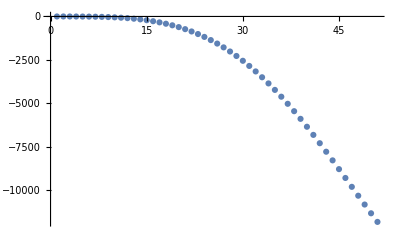

```mathematica
rmin=1.1*SubStar[r1];
rmax=5*SubStar[r1];
n=50;
Δr=(rmax-rmin)/n;
Table[hnnforplot//Chop,{r,rmin,rmax,Δr}];
ListPlot[%]
```

## 5. Metric Perturbations for Single Modes of Weyl Scalars

In this section we replicate the procedure of the preceding section with two modifications (1) we obtain the metric perturbation associated with a single mode of either Weyl scalar  and (2) instead of plotting a tetrad component  , we plot a Boyer-Lindquist coordinate component, namely .

As shown in sections 2.7 and 2.8 of the paper, one can choose the coefficients  and   so that the metric perturbation corresponds to a single mode in either of the Weyl scalars  and . These coefficients depend on the radial and angular Teukolsky-Starobinsky constants defined in section 2.4 of the paper.

```mathematica
calD[ω_,l_,m_]:=Module[{Subscript[λ, +2],t1,t2,t3,t4},
Subscript[λ, +2]=λ[2,ω,l,m];
t1=((Subscript[λ, +2]+4-(2 a^2 Λ)/3)(Subscript[λ, +2]+6-(4 a^2 Λ)/3)+4 a^2 Λ)^2;
t2=8 Ξ^2*a ω *(m -a*ω)*(Subscript[λ, +2]+4-2 a^2 Λ/3)*(5 Subscript[λ, +2]+26-16*a^2 Λ/3);
t3=96 Ξ^2*a^2*(Subscript[λ, +2]+4-2 a^2 Λ/3)*(ω^2-Λ/3*(m-ω*a)^2);
t4=144 Ξ^2*a^2*ω*(Ξ^2*ω*(m-ω*a)-2*a*Λ/3)*(m-ω*a);
t1+t2+t3+t4
]
calC[ω_,l_,m_]:=calD[ω,l,m]+(12 ω*Ξ*M)^2;

(* Angular constants *)
p1[c_,x_]:=x+6c+4*(1-2 a^2 Λ/3);
p2[c_,x_]:=x^2+2(4 c+5-3*a^2 Λ/3)x+4(3 c^2+4*(2-a^2 Λ/3)*c+2*(3-2*a^2 Λ/3+(a^2 Λ/3)^2));
p3[c_,x_]:=x^3-2(3 c-8+2*a^2 Λ/3)x^2-4(c^2+4*(2-a^2 Λ/3)*c-21+2*a^2 Λ/3-5*(a^2 Λ/3)^2)x+8(3 c^3-2*(4+a^2 Λ/3)c^2-(1-10*a^2 Λ/3+(a^2 Λ/3)^2)*c+2*(9+(a^2 Λ/3)^2-2*(a^2 Λ/3)^3));
Dhat[ω_,l_,m_]:=Module[{Subscript[λ, +2]},
Subscript[λ, +2]=λ[2,ω,l,m];
Which[
m>=2,Ξ^-2/((m+2)*(m+1)*m*(m-1))*calD[ω,l,m],
m==1,-1/(6*Ξ)p3[a*ω*Ξ,Subscript[λ, +2]],
m==0,p2[-a*ω*Ξ,Subscript[λ, +2]],
m==-1,-6*Ξ*p1[-a*ω*Ξ,Subscript[λ, +2]],
m<=-2,(m+1)*m*(m-1)*(m-2)*Ξ^2
]
]
DhatPrime[ω_,l_,m_]:=Module[{Subscript[λ, +2]},
Subscript[λ, +2]=λ[2,ω,l,m];
Which[
m>=2,(m+2)*(m+1)*m*(m-1)*Ξ^2,
m==1,-6*Ξ*p1[a*ω*Ξ,Subscript[λ, +2]],
m==0,p2[a*ω*Ξ,Subscript[λ, +2]],
m==-1,-1/(6*Ξ)p3[-a*ω*Ξ,Subscript[λ, +2]],
m<=-2,Ξ^-2/((m+1)*m*(m-1)*(m-2))calD[ω,l,m]
]
];

(* Radial constants *)
Γ[ω_,m_]:=Module[{σ,w},
σ=Δplist[[1]];
w=2*(ω-m*Subscript[Ω, 1])*Ξ*(r1^2+a^2);
(w+2 ⅈ σ)(w+ⅈ σ)w(w-ⅈ σ)
]
Γ̃[ω_,m_]:=Module[{σ,w},
σ=Δplist[[1]];
w=2*(ω-m*Subscript[Ω, 1])*Ξ*(r1^2+a^2);
(w-2 ⅈ σ)(w-ⅈ σ)w(w+ⅈ σ)
]
𝒞in[ω_,l_,m_]:=Γ[ω,m]
𝒞inPrime[ω_,l_,m_]:=calC[ω,l,m]/Γ[ω,m]
𝒞out[ω_,l_,m_]:=calC[ω,l,m]/Γ̃[ω,m]
𝒞outPrime[ω_,l_,m_]:=Γ̃[ω,m]
```

We define a symbolic conjugation function.

```mathematica
conjugate[exp_]:=Module[{},exp/.Complex[a_,b_]:> Complex[a,-b]];
```

We define four substitution rules that enforce a single mode of  in IRG/ORG or a single mode of  in IRG/ORG. These correspond to equations (2.45), (2.46), (2.52) and (2.53).

```mathematica
(********** Subscript[ψ, 0] in IRG *********)
Bexp=4/(αin*𝒞in[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]+αout *𝒞out[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]);
IRGWeyl0={A->0,Abar->0,B->Bexp,Bbar->conjugate[Bexp]};

(********** Subscript[ψ, 0] in ORG *********)
Aexp=(192 ⅈ (Subscript[ω, x]+ⅈ Subscript[ω, y]) M*Ξ)/calC[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m];
Bexp=(16conjugate[Dhat[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]])/conjugate[calC[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]] ;
ORGWeyl0={A->Aexp,Abar->conjugate[Aexp],B->Bexp,Bbar->conjugate[Bexp]};

(********** Subscript[ψ, 4] in IRG *********)
Aexp=-(192 ⅈ (Subscript[ω, x]+ⅈ Subscript[ω, y]) M*Ξ)/calC[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m];
Bexp=(16conjugate[DhatPrime[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]])/conjugate[calC[Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]];
IRGWeyl4={A->Aexp,Abar->conjugate[Aexp],B->Bexp,Bbar->conjugate[Bexp]};

(********** Subscript[ψ, 4] in ORG *********)
Bexp=64/conjugate[αin 𝒞inPrime[ω,l,m]+αout 𝒞outPrime[ω,l,m]];
ORGWeyl4={A->0,Abar->0,B->Bexp,Bbar->conjugate[Bexp]};
```

We import the Boyer-Lindquist components of a metric perturbation.

```mathematica
<<"./metric-perturbations/hIRGExpressions.mx"
```

We use the numerical parameters from the previous section. We substitute on  such that the metric perturbation corresponds to a single mode of . We set αin = 1, αout = 0 such that the radial function is made up exclusively of the ingoing solution, i.e.  . We then plot the results  in the  plane.

```mathematica
SubStar[αin]=1;
SubStar[αout]=0;
{hIRGBLExp[[1,1]]}/.IRGWeyl0;
%/.{ω->Subscript[ω, x]+ⅈ Subscript[ω, y],ωbar->Subscript[ω, x]-ⅈ Subscript[ω, y]};
%/.modeSub/.Λ->3 σ^2/L^2;
%/.{λ[2,Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]->SubStar[λ],λ[-2,Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]->SubStar[λ]+4,λ[-2,-Subscript[ω, x]+ⅈ Subscript[ω, y],l,-m]->Conjugate[SubStar[λ]]+4,λbar[-2,Subscript[ω, x]+ⅈ Subscript[ω, y],l,m]->Conjugate[SubStar[λ]]+4,λbar[-2,-Subscript[ω, x]+ⅈ Subscript[ω, y],l,-m]->SubStar[λ]+4};
%/.{M->SubStar[M],a->SubStar[a],L->SubStar[L],σ->SubStar[σ],σbar->Conjugate[SubStar[σ]],m->SubStar[m],ϵg->1,αin->SubStar[αin],αout->SubStar[αout],l->SubStar[l],Subscript[ω, x]->Subscript[ω, xstar],Subscript[ω, y]->Subscript[ω, ystar],r1->SubStar[r1],r2->SubStar[r2],r3->SubStar[r3],r4->SubStar[r4],r3bar->Conjugate[SubStar[r3]],r4bar->Conjugate[SubStar[r4]]};
%/.{ϕ->0.5,t->1.2};
plotComponents=%;
```

```mathematica
starttime=AbsoluteTime[];
θmin=π/4;
θmax=3 π/4;
rmin=1.1*SubStar[r1];
rmax=5*SubStar[r1];
nr=20;
nθ=20;
Δr=(rmax-rmin)/nr;
Δθ=(θmax-θmin)/nθ;
ParallelTable[{r,θ,plotComponents[[1]]//Chop},{r,rmin,rmax,Δr}, {θ,θmin,θmax,Δθ}];
ListPointPlot3D[%]
AbsoluteTime[]-starttime
```

-Graphics3D-

150.76028